### Layers

1

```mathematica
LinearLayer["Input"-> {1,"Real"},"Output"-> 2]
```

LinearLayer[<>]

```mathematica
LinearLayer[ "Input"-> {2,"Real"},"Output"-> {3,2}]
```

LinearLayer[<>]

3

```mathematica
LinearLayer["Input"-> 1,"Output"-> 1,"Weights"-> 1,"Biases"-> 2]
```

LinearLayer[<>]

```mathematica
4
```

```mathematica
NetInitialize[LinearLayer["Input"-> "Real","Output"-> "Real",LearningRateMultipliers->{"Biases"->1}]]
```

LinearLayer[<>]

```mathematica
5
```

```mathematica
NetInitialize[LinearLayer["Input"-> "Real","Output"-> "Real",LearningRateMultipliers->{"Biases"->1}],Method-> {"Xavier","Distribution"->"Normal"},RandomSeeding->888]
```

LinearLayer[<>]

```mathematica
6
```

```mathematica
LinearL=NetInitialize[LinearLayer[2, "Input"-> 1],RandomSeeding->888];
NetExtract[LinearL,#]&/@{"Weights","Biases"}//TableForm
```

NumericArray[…]
NumericArray[…]

```mathematica
7
```

```mathematica
TableForm[SetPrecision[{{Normal[NetExtract[LinearL,"Weights"]]},{Normal[NetExtract[LinearL,"Biases"]]}},3],TableHeadings->{{"Weights →","Biases →"},None}]
```

Weights → | -0.779
0.0435
Biases → | 0
0

```mathematica
8
```

```mathematica
LinearL[4]
```

{-3.11505,0.174007}

```mathematica
9
```

```mathematica
LinearL[{88,99}]
```

LinearLayer::invindata1: Data supplied to port "Input" was a length-2 vector of real numbers, but expected a length-1 vector of real numbers.

$Failed

```mathematica
10
```

```mathematica
LinearL[2,NetPortGradient["Input"]]
```

{-0.735261}

```mathematica
11
```

```mathematica
MeanSquaredLossLayer[]
```

MeanSquaredLossLayer[<>]

```mathematica
12
```

```mathematica
MeanSquaredLossLayer["Input"->{3,2},"Target"->{3,2}][Association["Input"->{{1,2},{2,1},{3,2}},"Target"->{{2,2},{1,1},{1,3}}]]
```

1.16667

```mathematica
13
```

```mathematica
LossLayer=MeanSquaredLossLayer["Input"->{3,2},"Target"->{3,2} ];
LossLayer@
<|"Input"->{{1,2},{2,1},{3,2}},"Target"->{{2,2},{1,1},{1,3}}|>
```

1.16667

```mathematica
14
```

```mathematica
Information[LossLayer]
```

Net Information

```mathematica
15
```

```mathematica
MeanSquaredLossLayer["Input"->"Real","Target"->"Real"]//Options
```

{BatchSize→Automatic,NetEvaluationMode→Test,RandomSeeding→Automatic,TargetDevice→CPU,WorkingPrecision→Real32}

```mathematica
16
```

```mathematica
{MeanSquaredLossLayer["Input"->"Varying","Target"->"Varying"],MeanSquaredLossLayer["Input"-> NetEncoder["Image"],"Target"-> NetEncoder["Image"]],MeanSquaredLossLayer["Input"->1,"Target"->1]}//Dataset
```

```mathematica
17
```

```mathematica
ElementwiseLayer[Tanh[#]&](* Altnernate form ElementwiseLayer[Tanh]*)
```

ElementwiseLayer[<>]

```mathematica
18
```

```mathematica
ElementwiseLayer[Tanh[#]&];
Table[%[i],{i,-5,5}]
```

{-0.999909,-0.999329,-0.995055,-0.964028,-0.761594,0.,0.761594,0.964028,0.995055,0.999329,0.999909}

```mathematica
19
```

```mathematica
TanhLayer=ElementwiseLayer[Tanh,"Input"-> "Real"]
```

ElementwiseLayer[<>]

```mathematica
20
```

```mathematica
RampLayer=ElementwiseLayer[Ramp,"Output"-> {1}](*or ElementwiseLayer["ReLU","Output"-> "Varying"]*)
```

ElementwiseLayer[<>]

```mathematica
21
```

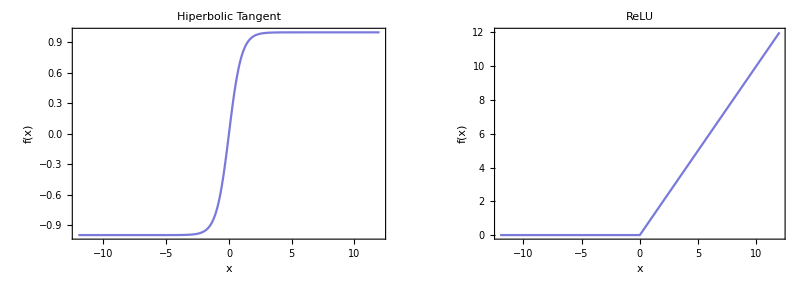

```mathematica
GraphicsRow@{Plot[TanhLayer[x,TargetDevice-> "CPU"],{x,-12,12},PlotLabel->"Hiperbolic Tangent",AxesLabel->{Style["x",Bold],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True],Plot[RampLayer[x,TargetDevice-> "CPU"],{x,-12,12},PlotLabel->"ReLU",AxesLabel->{Style["x",Bold],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True]}
```

```mathematica
22
```

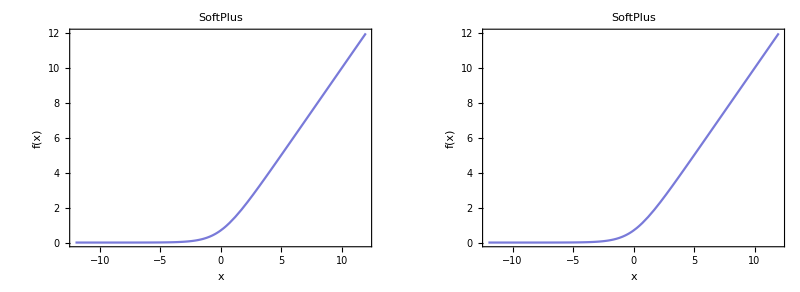

```mathematica
GraphicsRow@{Plot[ElementwiseLayer["SoftPlus"][x,TargetDevice-> "CPU"],{x,-12,12},PlotLabel->#1,AxesLabel->#2,PlotStyle->#3,Frame->#4],Plot[ElementwiseLayer[Log[Exp[#]+1]&][x,TargetDevice-> "CPU"],{x,-12,12},PlotLabel->#1,AxesLabel->#2,PlotStyle->#3,Frame->#4]}&["SoftPlus",{Style["x",Bold],Style["f(x)",Italic]},ColorData[97,25],True]
```

```mathematica
23
```

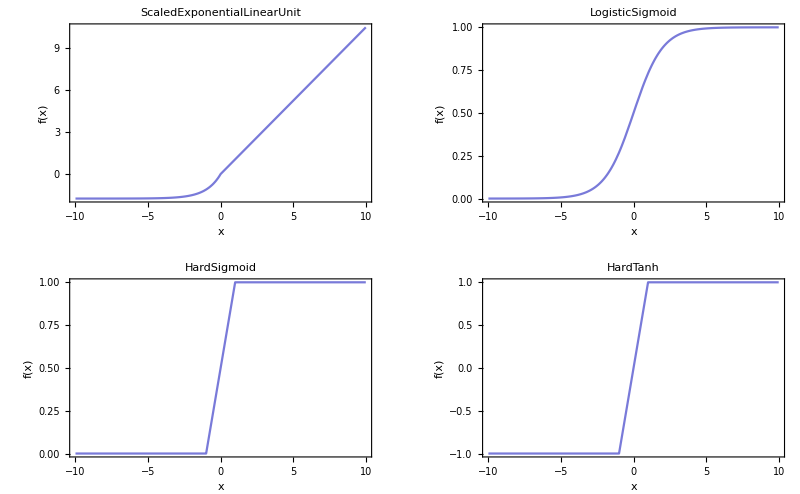

```mathematica
GraphicsGrid@{{Plot[ElementwiseLayer["ScaledExponentialLinearUnit"][i,TargetDevice-> #1],#2,AxesLabel->#3,PlotStyle->#4,Frame->#5,PlotLabel->"ScaledExponentialLinearUnit"],
Plot[ElementwiseLayer[LogisticSigmoid][i,TargetDevice-> #1],#2,AxesLabel->#3,PlotStyle->#4,Frame->#5,PlotLabel->"LogisticSigmoid"]},
{Plot[ElementwiseLayer["HardSigmoid"][i,TargetDevice-> #1],#2,AxesLabel->#3,PlotStyle->#4,Frame->#5,PlotLabel->"HardSigmoid"],
Plot[ElementwiseLayer["HardTanh"][i,TargetDevice-> #1],#2,AxesLabel->#3,PlotStyle->#4,Frame->#5,PlotLabel->"HardTanh"]}}&["CPU",{i,-10,10},{Style["x",Bold],Style["f(x)",Italic]},ColorData[97,25],True]
```

```mathematica
24
```

```mathematica
SFL=SoftmaxLayer["Input"-> 4,"Output"-> 4];
```

```mathematica
25
```

```mathematica
SetAccuracy[SFL[{9,8,7,6}],3]
```

{0.64,0.24,0.09,0.03}

```mathematica
26
```

```mathematica
SoftmaxLayer[1,"Input"->{3,2}];
SetPrecision[%[{{7,8},{8,7},{7,8}}],3]//MatrixForm
```

(0.212 | 0.422
0.576 | 0.155
0.212 | 0.422)

```mathematica
27
```

```mathematica
CrossEntropyLossLayer["Probabilities","Input"->3 ];
```

```mathematica
28
```

```mathematica
%[<|"Input"->{0.2,0.5,0.3},"Target"->{0.3,0.5,0.2}|>]
```

1.0702

```mathematica
29
```

```mathematica
CrossEntropyLossLayer["Binary","Input"-> 1];
%[<|"Input"-> 0.1,"Target"-> 0.9|>]
```

2.08286

### Encoders and Decoder

```mathematica
30
```

```mathematica
NetEncoder["Boolean"]
```

NetEncoder[<>]

```mathematica
31
```

```mathematica
Print["Booleans:",{%[True],%[False]}]
```

Booleans:{1,0}

```mathematica
32
```

```mathematica
NetEncoder[{"Class",{"Class X","Class Y"}}]
```

NetEncoder[<>]

```mathematica
33
```

```mathematica
Print["Classes:",%[Table[RandomChoice[{"Class X","Class Y"}],{i,10}]]]
```

Classes:{2,1,2,2,1,1,2,1,1,1}

```mathematica
34
```

```mathematica
NetEncoder[{"Class",{"Class X","Class Y","Class Z"},"UnitVector"}];
Print["Unit Vector:",%[Table[RandomChoice[{"Class X","Class Y","Class Z"}],{i,5}]]]
Print["MatrixForm:",%%[Table[RandomChoice[{"Class X","Class Y","Class Z"}],{i,5}]]//MatrixForm[#]&]
```

Unit Vector:{{0,1,0},{0,0,1},{0,1,0},{1,0,0},{1,0,0}}

MatrixForm:(0 | 0 | 1
0 | 0 | 1
1 | 0 | 0
0 | 1 | 0
1 | 0 | 0)

```mathematica
35
```

```mathematica
ElementwiseLayer[Sin,"Input"->NetEncoder["Boolean"]]
```

ElementwiseLayer[<>]

```mathematica
36
```

```mathematica
LinearLayer["Input"->NetEncoder[{"Class",{"Class X","Class Y"}}],"Output"-> "Scalar"]
```

LinearLayer[<>]

```mathematica
37
```

```mathematica
Table[NetEncoder[{"Image",{28,28},"ColorSpace"-> Color}],{Color,{"Grayscale","RGB"}}]
```

{NetEncoder[<>],NetEncoder[<>]}

```mathematica
38
```

```mathematica
ImgEncoder=NetEncoder[{"Image",{3,3},"ColorSpace"-> "CMYK"}];
Print["Numeric Matrix:",SetPrecision[%[ExampleData[{"TestImage","House"}]],3]//MatrixForm]
```

Numeric Matrix:((0.255
0.169
0.255) | (0.145
0.00392
0.0235) | (0.0784
0.0118
0.0275)
(0.153
0.196
0.129) | (0.2
0.31
0.255) | (0.259
0.349
0.306)
(0.0471
0.102
0.00784) | (0.165
0.322
0.165) | (0.263
0.384
0.176)
(0.161
0.263
0.184) | (0.255
0.408
0.478) | (0.325
0.388
0.569))

```mathematica
39
```

```mathematica
PoolLayer=PoolingLayer[{3,3},{2,2},PaddingSize->0,"Function"-> Max,"Input"-> NetEncoder[{"Image",{3,3},"ColorSpace"-> "CMYK"}](*Or ImgEncoder*)]
```

PoolingLayer[<>]

```mathematica
40
```

```mathematica
SetPrecision[PoolLayer[ExampleData[{"TestImage","House"}]],3]//MatrixForm
```

((0.255)
(0.349)
(0.384)
(0.569))

```mathematica
41
```

```mathematica
Decoder=NetDecoder[{"Class",CharacterRange["W","Z"]}]
```

NetDecoder[<>]

```mathematica
42
```

```mathematica
Decoder@{0.3,0.2,0.1,0.4}(*This is the same as Decoder[{0.3,0.2,0.1,0,4},"Decision"] *)
```

Z

```mathematica
43
```

```mathematica
TableForm[{Decoder[{0.3,0.2,0.1,0.4},"TopDecisions"-> 4](* or {"TopDecisions", 4} the same is for TopProbabilities*),
Decoder[{0.3,0.2,0.1,0.4},"TopProbabilities"->  4],
Decoder[{0.3,0.2,0.1,0.4},"Entropy"]},TableDirections->Column,TableHeadings->{{Style["TopDecisions",Italic],Style["TopProbabilities",Italic],Style["Entropy",Italic]},None}]
```

TopDecisions | Z | W | X | Y
TopProbabilities | Z→0.4 | W→0.3 | X→0.2 | Y→0.1
Entropy | 1.27985 |  |  |

```mathematica
44
```

```mathematica
NetDecoder[{"Class",CharacterRange["X","Z"],"InputDepth"->2}];
```

```mathematica
45
```

```mathematica
TableForm[{%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"TopDecisions"-> 3](* or {"TopDecisions", 4} the same is for TopProbabilities*),
%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"TopProbabilities"->  3],
%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"Entropy"]},TableDirections->Column,TableHeadings->{{Style["TopDecisions",Italic],Style["TopProbabilities",Italic],Style["Entropy",Italic]},None}]
```

TopDecisions | Z
Y
X | Y
X
Z
TopProbabilities | Z→0.6
Y→0.3
X→0.1 | Y→0.4
X→0.3
Z→0.3
Entropy | 0.897946 | 1.0889

```mathematica
46
```

```mathematica
SoftmaxLayer["Output"->NetDecoder[{"Class",{"X","Y","Z"}}]];
```

47

```mathematica
{%@{1,3,5},%[{1,3,5},"Probabilities"],%[{1,3,5},"Decision"]}
```

{Z,<|X→0.0158762,Y→0.11731,Z→0.866813|>,Z}

48

```mathematica
Img=ImageResize[ExampleData[{"TestImage","House"}],200]
```

-Graphics-

```mathematica
49
```

```mathematica
Encoder=NetEncoder[{"Image",{100,100},"ColorSpace"-> "RGB"}];
Decoder=NetDecoder[{"Image",ColorSpace-> "Grayscale"}];
```

```mathematica
50
```

```mathematica
Encoder[Img];
Decoder[%]
```

-Graphics-

```mathematica
51
```

```mathematica
ImageDimensions[%]
```

{100,100}

### Net Chains and Graphs

1

```mathematica
NetChain[{ElementwiseLayer[LogisticSigmoid@#&],ElementwiseLayer[Sin@#&]}]
```

NetChain[<>]

2

```mathematica
NetInitialize@NetChain[{3,4,12,Tanh},"Input"->1]
```

NetChain[<>]

```mathematica
3
```

```mathematica
NetInitialize@NetChain[{1,ElementwiseLayer[LogisticSigmoid@#&]},"Input"-> 1];
NetCH2=NetInitialize@NetAppend[%,{1,ElementwiseLayer[Cos[#]&]}]
```

NetChain[<>]

```mathematica
4
```

```mathematica
NetCH2[{{0},{2},{44}},NetEvaluationMode-> "Train",TargetDevice->"CPU",WorkingPrecision-> "Real64",RandomSeeding-> 8888](*use N@Cos[Sin[LogisticSigmoid[{0,2,44}]]] to check results*)
```

{{0.919044},{0.991062},{1.}}

```mathematica
5
```

```mathematica
NetInitialize@NetChain[<|"Linear Layer 1"->LinearLayer[3],
"Ramp"-> Ramp,"Linear Layer 2"->LinearLayer[4],"Logistic"-> ElementwiseLayer[LogisticSigmoid]|>,"Input"-> 3]
```

NetChain[<>]

```mathematica
6
```

```mathematica
NetExtract[%,"Logistic"];
```

```mathematica
7
```

```mathematica
Normal[NetCH2]//Column
```

LinearLayer[<>]
ElementwiseLayer[<>]
LinearLayer[<>]
ElementwiseLayer[<>]

```mathematica
8
```

```mathematica
chain1=NetChain[{12,SoftmaxLayer[]}];
chain2=NetChain[{1,ElementwiseLayer[Cos[#]&]}];
NestedChain=NetInitialize@NetChain[{chain1,chain2},"Input"-> 12]
```

NetChain[<>]

```mathematica
9
```

```mathematica
NetFlatten[NestedChain]
```

NetChain[<>]

```mathematica
10
```

```mathematica
NetInitialize@NetGraph[{ LinearLayer["Output"-> 1,"Input"-> 1],Cos,SummationLayer[]},{}]
```

NetGraph[<>]

```mathematica
11
```

```mathematica
Net1=NetInitialize@NetGraph[{ LinearLayer["Output"-> 2,"Input"-> 1],Cos,SummationLayer[]},{1-> 2-> 3}]
```

NetGraph[<>]

```mathematica
12
```

```mathematica
Net2=NetInitialize@NetGraph[{ LinearLayer["Output"-> 2,"Input"-> 1],Cos,SummationLayer[]},{1-> 3->2}]
```

NetGraph[<>]

```mathematica
13
```

```mathematica
NetInitialize@NetGraph[<|"Layer 1"-> LinearLayer[2,"Input"-> 1],"Layer 2"-> Cos,"Layer 3"-> SummationLayer[]|>,{"Layer 2"-> "Layer 1"-> "Layer 3"}]
```

NetGraph[<>]

```mathematica
14
```

```mathematica
NetInitialize@NetGraph[{ LinearLayer[3,"Input"-> 1],  LinearLayer[3,"Input"-> 2], LinearLayer[3,"Input"-> 1] ,TotalLayer[]},{NetPort["1st Input"]-> 1, NetPort["2nd Input"]-> 2,NetPort["3rd Input"]-> 3,{1,2,3}-> 4}](*Or NetInitialize@NetGraph[<|"L1"->  LinearLayer[3,"Input"-> 1],"L2"->   LinearLayer[3,"Input"-> 1], "L3"-> LinearLayer[3,"Input"-> 1] ,"Tot L"-> TotalLayer[]|>,{NetPort["1st Input"]-> "L1", NetPort["2nd Input"]-> "L2",NetPort["3rd Input"]->"L3",{"L1","L2","L3"} -> "Tot L"}]*)
```

NetGraph[<>]

```mathematica
15
```

```mathematica
%[<|"1st Input"-> 32.32,"2nd Input"-> {2,π},"3rd Input"-> 1|>]
```

{-41.7285,-11.2929,19.0044}

```mathematica
16
```

```mathematica
NetInitialize[NetGraph[{LinearLayer[1,"Input"-> 1],LinearLayer[1,"Input"-> 1],LinearLayer[1,"Input"-> 1],Ramp,ElementwiseLayer["ExponentialLinearUnit"],LogisticSigmoid},{1->4-> NetPort["Output1"],2->5-> NetPort["Output2"],3-> 6-> NetPort["Output3"]}],RandomSeeding->8888]
%[{1}]
```

NetGraph[<>]

<|Output1→{0.},Output2→{2.17633},Output3→{0.372197}|>

```mathematica
17
```

```mathematica
NetInitialize@NetGraph[{
LinearLayer[1,"Input"-> 1],
NetChain[{LinearLayer[1,"Input"-> 1],ElementwiseLayer[LogisticSigmoid[#]&]}],
NetChain[{LinearLayer[1,"Input"-> 1],Ramp}],
ElementwiseLayer["ExponentialLinearUnit"],
CatenateLayer[]
},{1->4,2->5,3-> 5,4-> 5}]
```

NetGraph[<>]

```mathematica
18
```

```mathematica
N1=NetGraph[{1,Ramp,2,LogisticSigmoid},{1-> 2,2-> 3,3-> 4}];
N2=NetChain[{3,SummationLayer[]}];
NetInitialize@NetGraph[{N2,N1},{2-> 1},"Input"-> 22]
```

NetGraph[<>]

```mathematica
19
```

```mathematica
Net=NetInitialize@NetGraph[{LinearLayer[10],Ramp,10,SoftmaxLayer[],TotalLayer[],ThreadingLayer[Times]},{1->2->3->4,{1,2,3}->5,{1,5}->6},"Input"->"Real"];
Information[Net,"SummaryGraphic"]
```

-Graphics-

```mathematica
20
```

```mathematica
{Dataset@Information[Net,"Arrays"],Dataset@Information[Net,"ArraysDimensions"],Dataset@Information[Net,"ArraysPositionList"]}//Dataset
```

```mathematica
21
```

```mathematica
{Information[Net,"InputPorts"],Information[Net,"OutputPorts"]}
```

{<|Input→Real|>,<|Output1→10,Output2→10|>}

```mathematica
22
```

```mathematica
Dataset@{Information[Net,"Layers"],Information[Net,"LayerTypeCounts"]}
```

```mathematica
23
```

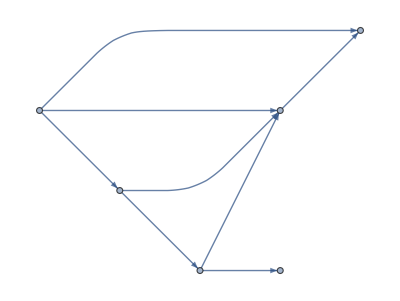
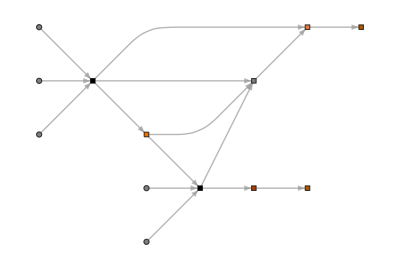
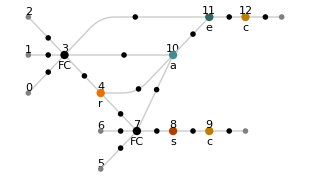
Layers Connection | NetGraph
-Graphics- | -Graphics-
MXNet Layer Graph | MXNet Ops Graph
-Graphics- | -Graphics-

```mathematica
Grid[{{Style["Layers Connection",Italic,20,ColorData[105,4]],Style["NetGraph",Italic,20,ColorData[105,4]]},{Information[Net,"LayersGraph"],Information[Net,"SummaryGraphic"]},
{Style["MXNet Layer Graph",Italic,20,ColorData[105,4]],Style["MXNet Ops Graph",Italic,20,ColorData[105,4]]},
{Information[Net,"MXNetNodeGraph"],Information[Net,"MXNetNodeGraphPlot"]}},Dividers->All,Background->{{{None,None}},{{Opacity[1,Gray],None}}}]
```

```mathematica
24
```

```mathematica
FileDirectory="C:\\Users\\My-pc\\Desktop\\MXNet Nets\\";
Export[FileNameJoin[{FileDirectory,"MxNet.json"}],Net,"MXNet","ArrayPath"-> Automatic,"SaveArrays"-> True]
```

C:\Users\lb-pc\Desktop\MXNet Nets\MxNet.json

```mathematica
25
```

```mathematica
FileNames[All,File@FileDirectory]
```

{C:\Users\lb-pc\Desktop\MXNet Nets\MxNet.json,C:\Users\lb-pc\Desktop\MXNet Nets\MxNet.params}

```mathematica
26
```

```mathematica
Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet","Net"},"ArrayPath"-> Automatic];
```

```mathematica
27
```

```mathematica
Row[Dataset[Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet",#}]]&/@{"ArrayAssociation","ArrayList","ArrayNames"}]
```

```mathematica
28
```

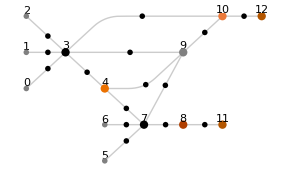

```mathematica
{Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet","NodeDataset"}],Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet","NodeGraphPlot"}]}//Row
```

```mathematica
29
```

```mathematica
NetModel["CapsNet Trained on MNIST Data"]
```

NetGraph[<>]